```mathematica
DSolve[y'[t] + y[t] == Sin[t], y[t], t]
```

{{y[t]→ⅇ^-t C[1]+1/2 (-Cos[t]+Sin[t])}}

```mathematica
DSolve[{y'[t] + y[t] == Sin[t], y[0] == 0}, y[t], t]
```

{{y[t]→-1/2 ⅇ^-t (-1+ⅇ^t Cos[t]-ⅇ^t Sin[t])}}

```mathematica
DE := y'[t] + y[t] == Sin[t]
```

```mathematica
y[t]+y'[t]==Sin[t]
```

y[t]+y'[t]==Sin[t]

```mathematica
solutions = Table[DSolve[{y[t]+y'[t]==Sin[t], y[0] == y0}, y[t], t], {y0, -2, 2}]
```

```mathematica
{{{y[t]->-1/2 ⅇ^-t (3+ⅇ^t Cos[t]-ⅇ^t Sin[t])}},{{y[t]->-1/2 ⅇ^-t (1+ⅇ^t Cos[t]-ⅇ^t Sin[t])}},{{y[t]->-1/2 ⅇ^-t (-1+ⅇ^t Cos[t]-ⅇ^t Sin[t])}},{{y[t]->-1/2 ⅇ^-t (-3+ⅇ^t Cos[t]-ⅇ^t Sin[t])}},{{y[t]->-1/2 ⅇ^-t (-5+ⅇ^t Cos[t]-ⅇ^t Sin[t])}}}
```

{{{y[t]→-1/2 ⅇ^-t (3+ⅇ^t Cos[t]-ⅇ^t Sin[t])}},{{y[t]→-1/2 ⅇ^-t (1+ⅇ^t Cos[t]-ⅇ^t Sin[t])}},{{y[t]→-1/2 ⅇ^-t (-1+ⅇ^t Cos[t]-ⅇ^t Sin[t])}},{{y[t]→-1/2 ⅇ^-t (-3+ⅇ^t Cos[t]-ⅇ^t Sin[t])}},{{y[t]→-1/2 ⅇ^-t (-5+ⅇ^t Cos[t]-ⅇ^t Sin[t])}}}

```mathematica
Plot[Evaluate[Table[y[t]/.solutions[[k]], {k, 5}]], {t, -1, 12}, AspectRatio->Automatic]
```

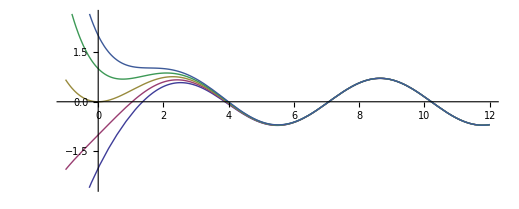

-Graphics-

```mathematica
DE2 = y'[t] == t/Cos[y[t]];
DE2
```

y'[t]==t Sec[y[t]]

```mathematica
y'[t]==t Sec[y[t]]
```

y'[t]==t Sec[y[t]]

```mathematica
GS2 = DSolve[DE2, y[t], t];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
GS2
```

{{y[t]→-ArcSin[1/2 (-t^2-2 C[1])]},{y[t]→ArcSin[1/2 (t^2+2 C[1])]}}

```mathematica
soln = DSolve[{DE2, y[0]==1}, y[t], t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[t]→-ArcSin[1/2 (-t^2-2 Sin[1])]},{y[t]→ArcSin[1/2 (t^2+2 Sin[1])]}}

```mathematica
p1 = Plot[y[t]/.soln[[1]], {t, -0.2, 0.2}];
```

```mathematica
p2 = Plot[y[t]/.soln[[2]], {t, -0.2, 0.2}];
```

```mathematica
Show[p1,p2]
```

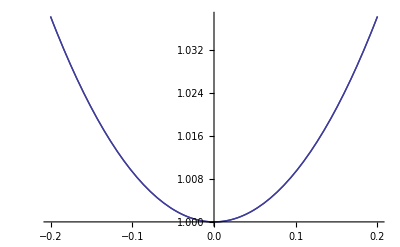
```mathematica
-Graphics-

p2
```

-Graphics-

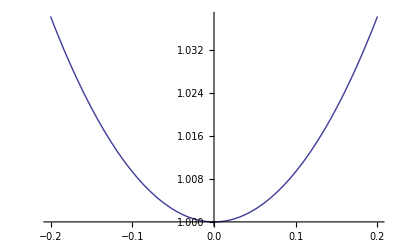

```mathematica
p1
```

-Graphics-